# Evolving to Oscillate

## Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Evolution

```mathematica
evol = Transpose[Import["evol.dat"]];
```

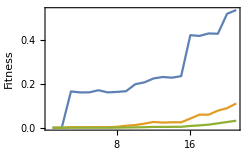

```mathematica
ListLinePlot[evol,Frame->True,FrameLabel->{"Generations","Fitness"},PlotRange->All,ImageSize->250]
```

## Performance with Learning

```mathematica
t = Import["osc_perf_learning.dat"];
```

```mathematica
final=Length[Transpose[t]];
```

```mathematica
N[Count[Transpose[t][[final]]-Transpose[t][[1]],u_/;u>0.0]/Length[t]]
```

1.

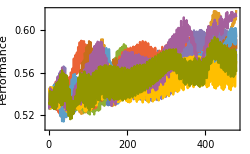
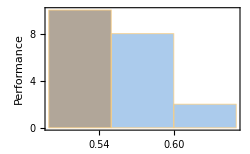
-Graphics-A
-Graphics-B

```mathematica
panelA = ListLinePlot[t,PlotRange->All,Frame->True,FrameLabel->{"Time","Performance"},ImageSize->250];
panelB =Histogram[{Transpose[t][[1]],Transpose[t][[final]]},PlotRange->All,Frame->True,FrameLabel->{"Time","Performance"},ChartStyle->"SouthwestColors",FrameLabel->{"Final performance","Relative frequency"},ImageSize->250] ;
charts={panelA,panelB};
labels=CharacterRange["A","Z"][[;;2]];
panels=Partition[Panel[#,Style[#2,14],{{Left,Top}},Appearance->"Frameless",Background->White]&@@@Transpose[{charts,labels}],1];
Grid[panels,Alignment->{Left,Top}]
```